# Equation of the line passing through a point with a slope

```mathematica
Subscript[x, P_]:=P[[1]];Subscript[y, P_]:=P[[2]];
```

```mathematica
A={2,3};
```

```mathematica
m=2;
```

```mathematica
y[x_]=m(x-Subscript[x, A])+Subscript[y, A]//Simplify
```

-1+2 x

```mathematica
PointA=ListPlot[{A},PlotRange->{{-5,5},{-5,5}},MeshStyle->Red,PlotMarkers->{Automatic,Medium},AspectRatio->1];
```

```mathematica
Droite=Plot[y[x],{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1];
```

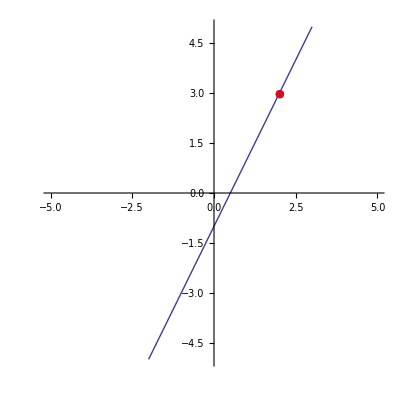

```mathematica
Show[PointA,Droite]
```